```mathematica
Integrate[x^2*ⅇ^-x,x]
```

ⅇ^-x (-2-2 x-x^2)

-2 x+2 ArcTan[x]+x Log[1+x^2]

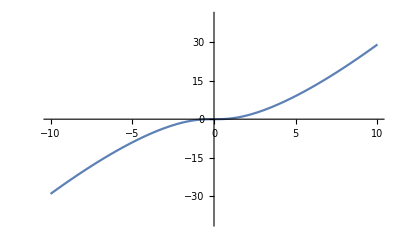

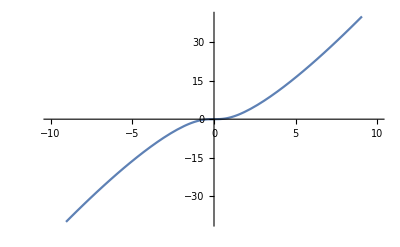

```mathematica
Integrate[Log[1+x^2],x]
Plot[-2 x+2 ArcTan[x]+x Log[1+x^2],{x,-10,10},PlotRange->{-40,40}]
Plot[x*Log[1+x^2],{x,-10,10},PlotRange->{-40,40}]
```

```mathematica
D[(x*Log[1+x^2]), x]
```

(2 x^2)/(1+x^2)+Log[1+x^2]

```mathematica
x===x+1-1
```

True

```mathematica
Integrate[ArcSin[x],x]
```

√(1-x^2)+x ArcSin[x]

```mathematica
TrigToExp[√(1-x^2)+x ArcSin[x]]
```

√(1-x^2)-ⅈ x Log[ⅈ x+√(1-x^2)]

```mathematica
Integrate[x/(√(1-x^2)),x]
```

-√(1-x^2)

```mathematica
Integrate[x/(Cos[x])^2,x]
```

Log[Cos[x]]+x Tan[x]

```mathematica
WolframAlpha["integrate x/(cos(x)^2)",{{"IndefiniteIntegral",2},"Content"},PodStates->{"IndefiniteIntegral__Step-by-step solution"}]
```

Take the integral:
∫x sec^2(x)ⅆx
For the integrand x sec^2(x), integrate by parts, ∫fⅆg==f g-∫gⅆf, where 
 f==x,    ⅆg==sec^2(x) ⅆx,
ⅆf== ⅆx,     g==tan(x):
 == x tan(x)-∫tan(x)ⅆx
Rewrite tan(x) as (sin(x))/(cos(x)):
 == x tan(x)-∫(sin(x))/(cos(x))ⅆx
For the integrand (sin(x))/(cos(x)), substitute u==cos(x) and ⅆu==-sin(x) ⅆx:
 == x tan(x)-∫-1/uⅆu
Factor out constants:
 == x tan(x)+∫1/u ⅆu
The integral of 1/u is log(u):
 == log(u)+x tan(x)+constant
Substitute back for u==cos(x):
Answer: | 
 |  == x tan(x)+log(cos(x))+constant

```mathematica
WolframAlpha["integrate arctan(x)/(x^3)",{{"IndefiniteIntegral",2},"Content"},PodStates->{"IndefiniteIntegral__Step-by-step solution"}]
```

Take the integral:
∫(tan^-1(x))/x^3 ⅆx
For the integrand (tan^-1(x))/x^3, integrate by parts, ∫fⅆg==f g-∫gⅆf, where 
 f==tan^-1(x),    ⅆg==1/x^3 ⅆx,
ⅆf==1/(x^2+1) ⅆx,     g==-1/(2 x^2):
 == -(tan^-1(x))/(2 x^2)-∫-1/(2 x^2 (x^2+1))ⅆx
Factor out constants:
 == -(tan^-1(x))/(2 x^2)+1/2∫1/(x^2 (x^2+1))ⅆx
For the integrand 1/(x^2 (x^2+1)), use partial fractions:
 == -(tan^-1(x))/(2 x^2)+1/2∫(1/x^2-1/(x^2+1))ⅆx
Integrate the sum term by term and factor out constants:
 == -(tan^-1(x))/(2 x^2)-1/2∫1/(x^2+1)ⅆx+1/2∫1/x^2 ⅆx
The integral of 1/(x^2+1) is tan^-1(x):
 == -1/2 tan^-1(x)-(tan^-1(x))/(2 x^2)+1/2∫1/x^2 ⅆx
The integral of 1/x^2 is -1/x:
 == -(tan^-1(x))/(2 x^2)-1/(2 x)-1/2 tan^-1(x)+constant
Which is equal to:
Answer: | 
 |  == -(x^2 tan^-1(x)+x+tan^-1(x))/(2 x^2)+constant